# Primordial Black Holes Generated by the Non-Minimal Spectator Field

D.-S. Meng, C. Yuan, and Q.-G. Huang, Primordial Black Holes Generated by the Non-Minimal Spectator Field, arXiv:2212.03577.

CavanLee

## Solving Mukhanov-Sasaki Equation

### Setups

```mathematica
ClearAll["Global`*"]
```

```mathematica
(*定义参数*)
Δ=0.1;
Λ=0.01;
ξ=0.001;
AG=0.99;
AR=0.99;
AO=0.15;
H=1;
τ0=-1;
a[x_]:=-1/(H x τ0);(*Scale Factor in de Sitter Space*)
k0=-1/τ0;
```

### Plot Model G, R & O

```mathematica
(*Phenomenoligical Forms*)
fG[x_]:=1-AG Exp[-(x-1)^2/(2 Δ^2)];
fR[x_]:=1-AR/2 (Tanh[(x-(1-Δ/2))/Λ]-Tanh[(x-(1+Δ/2))/Λ]);
fO[x_]:=1-AO/2 (Tanh[(x-(1-Δ/2))/Λ]-Tanh[(x-(1+Δ/2))/Λ]) Sin[(x-1)/ξ];
```

```mathematica
fig1=Plot[{fG[x],fR[x],fO[x]},{x,0.0,3.0},PlotRange->Full,PlotTheme->"Scientific",PlotLegends->Placed[LineLegend[{"Model G","Model R","Model O"},LegendFunction->(Framed[#,RoundingRadius->8,FrameStyle->LightGray]&),LegendMargins->0,LegendMarkerSize->{20,5}],{0.14,0.2}],FrameLabel->{"τ/τ_*","f_G, f_R, f_O"},LabelStyle->{Directive[Black,Bold,FontFamily->"Helvetica",FontSize->10]},PlotPoints->10000 ];
zoomfig=Plot[{fG[x],fR[x],fO[x]},{x,0,3},PlotRange->{{0.90,1.10},{0.8,1.18}},PlotTheme->"Scientific",PlotPoints->10000,LabelStyle->{Directive[Black,Bold,FontFamily->"Helvetica",FontSize->10]},Frame->True,FrameTicks->{{{0.9,1.0,1.1},None},{Automatic,None}},FrameTicksStyle->Directive[FontSize->8]];
FIG1=Show[fig1,Graphics[{FaceForm[None],EdgeForm[Directive[Gray]],Rectangle[{0.9,0.8},{1.1,1.18}],Gray,Dashed,Line[{{0.9,1.18},{1.424,0.75}}],Gray,Dashed,Line[{{1.1,1.18},{2.942,0.75}}]}],Epilog->Inset[zoomfig,{2.15,0.4}]];
```

### NDSolve M-S equations and Calculate Power spectra to each Model

#### Model G

```mathematica
afG[x_]:=a[x]*fG[x];
term[x_]:=D[afG[x],{x,2}]/afG[x];
```

```mathematica
resultG1=ParallelTable[Module[{sol,𝒫},sol=NDSolveValue[{φ''[x]+((k/k0)^2-term[x])*φ[x]==0,φ[10^5]==1/Sqrt[2*k],φ'[10^5]==I Sqrt[k/2]},φ,{x,10^-10,10^5}];
𝒫=2*(k)^3*Abs[sol[10^-10]/(-fG[10^-10]/-10^-10)]^2;
{k,𝒫}],{k,0.01,0.1,0.0001}];
ListLogLogPlot[resultG1,Joined->True,PlotRange->All];
```

```mathematica
resultG2=ParallelTable[Module[{sol,𝒫},sol=NDSolveValue[{φ''[x]+((k/k0)^2-term[x])*φ[x]==0,φ[10^5]==1/Sqrt[2*k],φ'[10^5]==I Sqrt[k/2]},φ,{x,10^-10,10^5}];
𝒫=2*(k)^3*Abs[sol[10^-10]/(-fG[10^-10]/-10^-10)]^2;
{k,𝒫}],{k,0.1,1,0.01}];
ListLogLogPlot[resultG2,Joined->True,PlotRange->All];
```

```mathematica
resultG3=ParallelTable[Module[{sol,𝒫},sol=NDSolveValue[{φ''[x]+((k/k0)^2-term[x])*φ[x]==0,φ[100]==1/Sqrt[2*k],φ'[100]==I Sqrt[k/2]},φ,{x,10^-10,100}];
𝒫=2*(k)^3*Abs[sol[10^-10]/(-fG[10^-10]/-10^-10)]^2;
{k,𝒫}],{k,1,10,0.01}];
ListLogLogPlot[resultG3,Joined->True,PlotRange->All];
```

```mathematica
resultG4=ParallelTable[Module[{sol,𝒫},sol=NDSolveValue[{φ''[x]+((k/k0)^2-term[x])*φ[x]==0,φ[1000]==1/Sqrt[2*k],φ'[1000]==I Sqrt[k/2]},φ,{x,10^-10,1000}];
𝒫=2*(k)^3*Abs[sol[10^-10]/(-fG[10^-10]/-10^-10)]^2;
{k,𝒫}],{k,10,100,0.1}];
ListLogLogPlot[resultG4,Joined->True,PlotRange->All];
```

```mathematica
resultG5=ParallelTable[Module[{sol,𝒫},sol=NDSolveValue[{φ''[x]+((k/k0)^2-term[x])*φ[x]==0,φ[100]==1/Sqrt[2*k],φ'[100]==I Sqrt[k/2]},φ,{x,10^-10,100}];
𝒫=2*(k)^3*Abs[sol[10^-10]/(-fG[10^-10]/-10^-10)]^2;
{k,𝒫}],{k,100,1000,5}];
ListLogLogPlot[resultG5,Joined->True,PlotRange->All];
```

```mathematica
resultG=Join[resultG1,resultG2,resultG3,resultG4,resultG5];
ListLogLogPlot[resultG,Joined->True,PlotRange->All];
```

#### Model R

```mathematica
afR[x_]:=a[x]*fR[x];
termR[x_]:=D[afR[x],{x,2}]/afR[x];
```

```mathematica
resultR1=ParallelTable[Module[{sol,𝒫},sol=NDSolveValue[{φ''[x]+((k/k0)^2-termR[x])*φ[x]==0,φ[10^5]==1/Sqrt[2*k],φ'[10^5]==I Sqrt[k/2]},φ,{x,10^-10,10^5}];
𝒫=2*k^3*Abs[sol[10^-10]/(-fR[10^-10]/-10^-10)]^2;
{k,𝒫}],{k,0.01,0.1,0.0001}];
ListLogLogPlot[resultR1,Joined->True,PlotRange->All];
```

```mathematica
resultR2=ParallelTable[Module[{sol,𝒫},sol=NDSolveValue[{φ''[x]+((k/k0)^2-termR[x])*φ[x]==0,φ[100]==1/Sqrt[2*k],φ'[100]==I Sqrt[k/2]},φ,{x,10^-10,100}];
𝒫=2*k^3*Abs[sol[10^-10]/(-fR[10^-10]/-10^-10)]^2;
{k,𝒫}],{k,0.1,1,0.01}];
ListLogLogPlot[resultR2,Joined->True,PlotRange->All];
```

```mathematica
resultR3=ParallelTable[Module[{sol,𝒫},sol=NDSolveValue[{φ''[x]+((k/k0)^2-termR[x])*φ[x]==0,φ[100]==1/Sqrt[2*k],φ'[100]==I Sqrt[k/2]},φ,{x,10^-10,100}];
𝒫=2*k^3*Abs[sol[10^-10]/(-fR[10^-10]/-10^-10)]^2;
{k,𝒫}],{k,1,10,0.01}];
ListLogLogPlot[resultR3,Joined->True,PlotRange->All];
```

```mathematica
resultR4=ParallelTable[Module[{sol,𝒫},sol=NDSolveValue[{φ''[x]+((k/k0)^2-termR[x])*φ[x]==0,φ[100]==1/Sqrt[2*k],φ'[100]==I Sqrt[k/2]},φ,{x,10^-10,100}];
𝒫=2*k^3*Abs[sol[10^-10]/(-fR[10^-10]/-10^-10)]^2;
{k,𝒫}],{k,10,100,0.1}];
ListLogLogPlot[resultR4,Joined->True,PlotRange->All];
```

```mathematica
resultR5=ParallelTable[Module[{sol,𝒫},sol=NDSolveValue[{φ''[x]+((k/k0)^2-termR[x])*φ[x]==0,φ[100]==1/Sqrt[2*k],φ'[100]==I Sqrt[k/2]},φ,{x,10^-10,100}];
𝒫=2*k^3*Abs[sol[10^-10]/(-fR[10^-10]/-10^-10)]^2;
{k,𝒫}],{k,100,1000,5}];
ListLogLogPlot[resultR5,Joined->True,PlotRange->All];
```

```mathematica
resultR=Join[resultR1,resultR2,resultR3,resultR4,resultR5];
ListLogLogPlot[resultR,Joined->True,PlotRange->All];
```

#### Model O

```mathematica
afO[x_]:=a[x]*fO[x];
termO[x_]:=D[afO[x],{x,2}]/afO[x];
```

```mathematica
resultO1=ParallelTable[Module[{sol,𝒫},sol=NDSolveValue[{φ''[x]+((k/k0)^2-termO[x])*φ[x]==0,φ[10^5]==1/Sqrt[2*k],φ'[10^5]==I Sqrt[k/2]},φ,{x,10^-10,10^5}];
𝒫=2*k^3*Abs[sol[10^-10]/(-fO[10^-10]/-10^-10)]^2;
{k,𝒫}],{k,0.01,0.1,0.001}];
ListLogLogPlot[resultO1,Joined->True,PlotRange->All];
```

```mathematica
resultO2=ParallelTable[Module[{sol,𝒫},sol=NDSolveValue[{φ''[x]+((k/k0)^2-termO[x])*φ[x]==0,φ[100]==1/Sqrt[2*k],φ'[100]==I Sqrt[k/2]},φ,{x,10^-10,100}];
𝒫=2*k^3*Abs[sol[10^-10]/(-fO[10^-10]/-10^-10)]^2;
{k,𝒫}],{k,0.1,1,0.1}];
ListLogLogPlot[resultO2,Joined->True,PlotRange->All];
```

```mathematica
resultO3=ParallelTable[Module[{sol,𝒫},sol=NDSolveValue[{φ''[x]+((k/k0)^2-termO[x])*φ[x]==0,φ[100]==1/Sqrt[2*k],φ'[100]==I Sqrt[k/2]},φ,{x,10^-10,100}];
𝒫=2*k^3*Abs[sol[10^-10]/(-fO[10^-10]/-10^-10)]^2;
{k,𝒫}],{k,1,10,0.1}];
ListLogLogPlot[resultO3,Joined->True,PlotRange->All];
```

```mathematica
resultO4=ParallelTable[Module[{sol,𝒫},sol=NDSolveValue[{φ''[x]+((k/k0)^2-termO[x])*φ[x]==0,φ[100]==1/Sqrt[2*k],φ'[100]==I Sqrt[k/2]},φ,{x,10^-10,100}];
𝒫=2*k^3*Abs[sol[10^-10]/(-fO[10^-10]/-10^-10)]^2;
{k,𝒫}],{k,10,100,0.1}];
ListLogLogPlot[resultO4,Joined->True,PlotRange->All];
```

```mathematica
resultO5=ParallelTable[Module[{sol,𝒫},sol=NDSolveValue[{φ''[x]+((k/k0)^2-termO[x])*φ[x]==0,φ[100]==1/Sqrt[2*k],φ'[100]==I Sqrt[k/2]},φ,{x,10^-10,100}];
𝒫=2*k^3*Abs[sol[10^-10]/(-fO[10^-10]/-10^-10)]^2;
{k,𝒫}],{k,100,1000,5}];
ListLogLogPlot[resultO5,Joined->True,PlotRange->All];
```

```mathematica
resultO=Join[resultO1,resultO2,resultO3,resultO4,resultO5];
ListLogLogPlot[resultO,Joined->True,PlotRange->All];
```

#### Plot power spectra

```mathematica
FIG2=ListLogLogPlot[{resultG,resultR,resultO},Joined->True,PlotRange->All,PlotTheme->"Scientific",PlotLegends->Placed[LineLegend[{"Model G","Model R","Model O"},LegendFunction->(Framed[#,RoundingRadius->8,FrameStyle->LightGray]&),LegendMargins->0,LegendMarkerSize->{18,5}],{0.14,0.75}],{FrameLabel->{"k/k_*","𝒫_δχ(k)/(H/(2  π))^2"},LabelStyle->{Directive[Black,Bold,FontFamily->"Arial",FontSize->10]}},PlotStyle->Thickness[0.004]];
```

## Export results

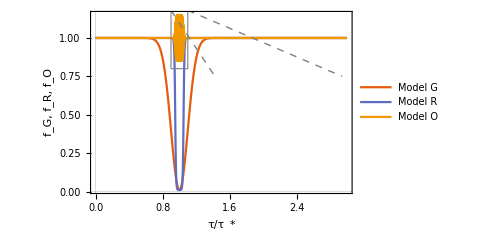

```mathematica
FIG1
```

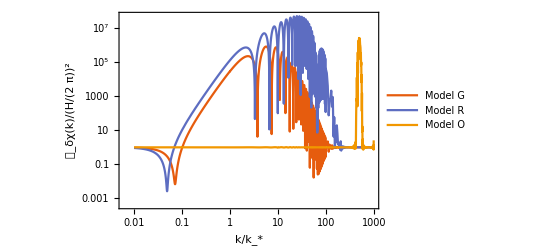

```mathematica
FIG2
```

```mathematica
Export["D:\\Research\\PBHs\\MMA\\FIG1.pdf",FIG1,ImageResolution->1200];
Export["D:\\Research\\PBHs\\MMA\\FIG2.png",FIG2,ImageResolution->660];
```